```mathematica
AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace2\\NumberTheory"];
<<NumberTheory`
```

```mathematica
ComplexAnalysis`BranchPoints[√(z^2-1),z]
ComplexAnalysis`BranchCuts[√(z^2-1),z]
```

{-1,1,ComplexInfinity}

(-1<Re[z]<0&&Im[z]==0)||Re[z]==0||(0<Re[z]<1&&Im[z]==0)

## Topic

### Definition / Theorem

This is text.

#### Example

# Notes CAN

tmp

## temp

### Definition / Theorem

#### Example

Complex Integration

## Visualize Function

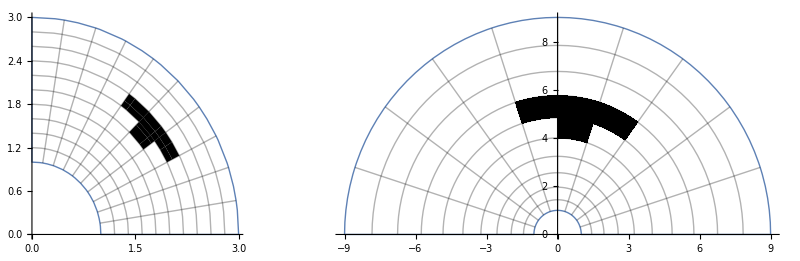

```mathematica
F[z_]:=z^2;
t1=0;
t2=Pi/2;
r1=1;
r2=3;
dt=(t2-t1)/10;
dr=(r2-r1)/10;

GraphicsRow[With[{z=r Exp[I t],col=Black},
ParametricPlot[ReIm@#[z],{r,r1,r2},{t,t1,t2},
Mesh->9,
MeshShading->ArrayPad[{{None,col},{col,col},{None,col}},{{3,4},{5,3}},None],
Frame->False,
AxesOrigin->{0,0}]]&/@{Identity,F}]
```

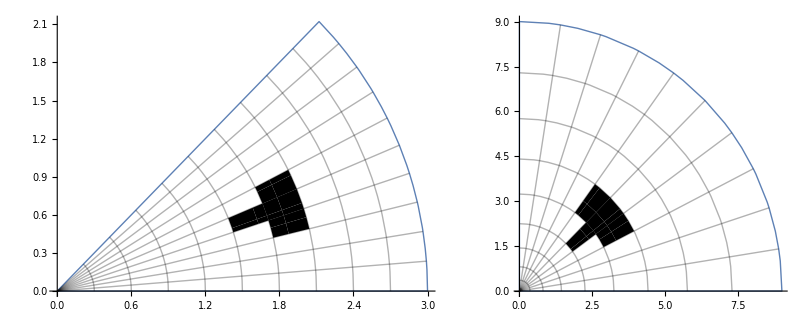

```mathematica
ClearAll[t1,t2,r1,r2,dt,dr]
F[z_]:=z^2;
t1=0;
t2=Pi/4;
r1=0;
r2=3;
GraphicsRow[With[{z=r Exp[I t],col=Black},
ParametricPlot[ReIm@#[z],{r,r1,r2},{t,t1,t2},
Mesh->9,
MeshShading->ArrayPad[{{None,col},{col,col},{None,col}},{{3,4},{5,3}},None],
Frame->False,
AxesOrigin->{0,0}]]&/@{Identity,F}]
```

## Contour Integral

### Definition / Theorem

#### Example

```mathematica
cContourIntegral[1/z,z,path[4]]//Expand
```

2 ⅈ π